# Code to plot from C-program output

0

10

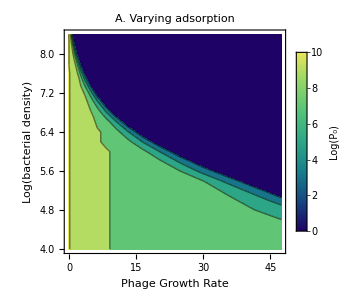
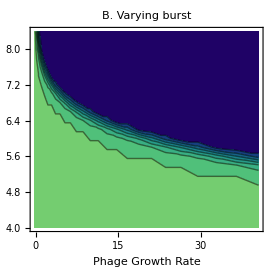

```mathematica
(*Export["Box Sync/mss/selfing/mpc30.csv",m2]*)

(*Import["/Users/bull/Box\ Sync/mss/phage_decay/cfiles/2patch1.csv"];*)
(*Import["/Users/bull/Box\ Sync/mss/phage_decay/cfiles/out1E6.csv"];*)
data1=Import["/Users/bull/Box Sync/mss/jenn/contour_noK.csv","CSV",HeaderLines->2];
data2=Import["/Users/bull/Box Sync/mss/jenn/contour_noK_b.csv","CSV",HeaderLines->2];
(*data1
data2*)
(*data2 = data1[[All,{1,8}]];*)
(*Step 2:Determine the overall value range*)
minVal=0;
maxVal=10;
fullRange={minVal,maxVal};

minVal
maxVal
(*data1*)
(*Step 3:Plot with a shared scale*)
plot1=ListContourPlot[data1,ColorFunction->ColorData[{"BlueGreenYellow",fullRange}],
Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->22,Black},ImageSize->300,ColorFunctionScaling->False,PlotLegends->None,FrameLabel->{Style["Phage Growth Rate",20],Style["Log(bacterial density)",20]},PlotLabel->"A. Varying adsorption"];
plot2=ListContourPlot[data2,ColorFunction->ColorData[{"BlueGreenYellow",fullRange}],
FrameLabel->{Style["Phage Growth Rate",20]},Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->22,Black},
ImageSize->274,ColorFunctionScaling->False,PlotLegends->None,PlotLabel->"B. Varying burst"];

(*Step 4:Display the plots and a single legend*)
legend=BarLegend[{"BlueGreenYellow",fullRange},LegendLabel->"Log(P_0)"];
Legended[Row[{plot1,plot2},Spacer[20]],legend]
```